Genez, Inc.
9617 Black Watch Court
Charlotte, NC 28277

February 5, 2021

To: Chief Scientist, Center for Bioinformatics
From: Aakriti Lakshmanan
Subj: Analysis of Six Drug Dataset

## Summary and Introduction

### Abstract:

As requested in the Scope of Work of January 26, 2011, we have conducted a basic analysis of a six-drug dataset.

### Introduction/Background Information:

In this work we obtained a dataset of six drugs from the North Carolina High School Computational Chemistry server database. The compounds were numbered 1 through 6, and contained seven quantum chemical descriptors:

Energy

Dipole moment (polarity)

Highest Occupied Molecular Orbital (HOMO)

Lowest Unoccupied Molecular Orbital (LUMO)

HOMO/LUMO gap (difference between HOMO and LUMO)

Electrostatic Potential minimum value

Electrostatic Potential maximum value

K_i, the binding affinity of the receptor

## Methodology

In this work, we obtained and extracted the data from the North Carolina High School Computational Chemistry server database, and then performed descriptive statistical analyses, data visualization, and regression analyses of the dataset.

## Results

Here are the results for this Scope of Work:

#### Data Import and Extraction:

```mathematica
drugData = Import["/Users/aakritilakshmanan/Downloads/sixdrugqsar.csv"];
Grid[drugData, Frame -> All]
header = drugData[[1]];
drugData = Delete[drugData,1];
{cmpd,energy, dipole, homo, lumo, homolumo, elpotmin, elpotmax, ki} = Transpose[drugData]
```

Cmpd | Energy | Dipole | HOMO | LUMO | HOMOLUMO Gap | ElPotMin | ElPotMax | Ki
1 | -89.8594 | 5.035 | -0.21657 | 0.0082 | 0.22477 | -2.82719 | -1.13415 | 7.2
2 | -71.1931 | 4.548 | -0.22868 | -0.00362 | 0.22506 | -2.68957 | -1.08135 | 6.5
3 | -118.553 | 4.683 | -0.21866 | 0.00832 | 0.22698 | -3.23607 | -1.03287 | 0.79
4 | -159.645 | 4.206 | -0.2234 | 0.00521 | 0.22861 | -3.01286 | -1.01623 | 8.4
5 | -119.092 | 3.963 | -0.22772 | 0.00753 | 0.23525 | -3.05296 | -0.9378 | 0.57
6 | -123.927 | 4.585 | -0.22783 | 0.00979 | 0.23762 | -3.23386 | -1.00829 | 0.55

{{1,2,3,4,5,6},{-89.8594,-71.1931,-118.553,-159.645,-119.092,-123.927},{5.035,4.548,4.683,4.206,3.963,4.585},{-0.21657,-0.22868,-0.21866,-0.2234,-0.22772,-0.22783},{0.0082,-0.00362,0.00832,0.00521,0.00753,0.00979},{0.22477,0.22506,0.22698,0.22861,0.23525,0.23762},{-2.82719,-2.68957,-3.23607,-3.01286,-3.05296,-3.23386},{-1.13415,-1.08135,-1.03287,-1.01623,-0.9378,-1.00829},{7.2,6.5,0.79,8.4,0.57,0.55}}

```mathematica
Median[drugData[[1]]]
```

0.0082

### Data Analysis:

Descriptive Statistics:

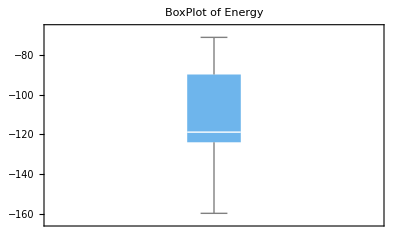
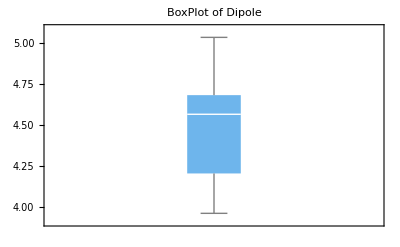
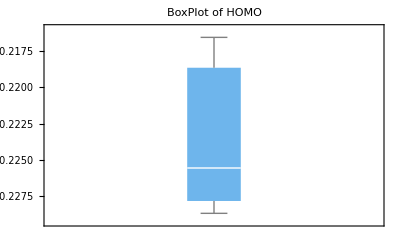
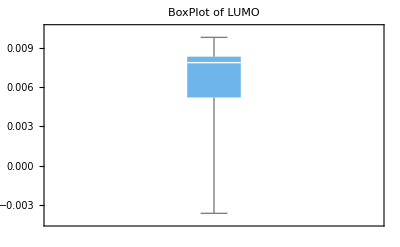
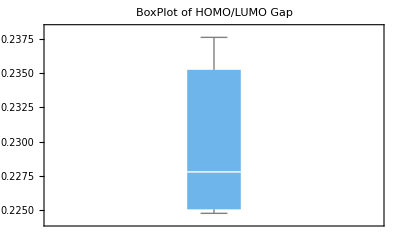
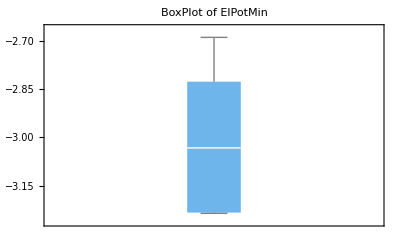
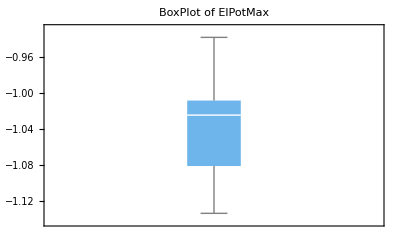
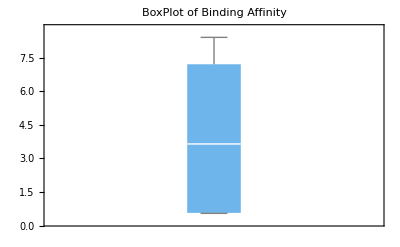
□ | Median | Min | Max | Boxplot
Energy | -118.822 | -159.645 | -71.1931 | -Graphics-
Dipole | 4.5665 | 3.963 | 5.035 | -Graphics-
HOMO | -0.22556 | -0.22868 | -0.21657 | -Graphics-
LUMO | 0.007865 | -0.00362 | 0.00979 | -Graphics-
HOMOLUMO Gap | 0.227795 | 0.22477 | 0.23762 | -Graphics-
ElPotMin | -3.03291 | -3.23607 | -2.68957 | -Graphics-
ElPotMax | -1.02455 | -1.13415 | -0.9378 | -Graphics-
b | 3.645 | 0.55 | 8.4 | -Graphics-

```mathematica
Grid[{{□, Style["Median", Bold], Style["Min", Bold], Style["Max", Bold], Style["Boxplot", Bold]}, {Style[header[[2]],Bold], Median[energy], Min[energy], Max[energy], BoxWhiskerChart[energy, PlotLabel -> "BoxPlot of Energy",LabelStyle->{FontFamily->"Times New Roman",11,GrayLevel[0]}, ChartStyle-> "Pastel"]}, {Style[header[[3]],Bold], Median[dipole], Min[dipole], Max[dipole], BoxWhiskerChart[dipole, PlotLabel -> "BoxPlot of Dipole",LabelStyle->{FontFamily->"Times New Roman",11,GrayLevel[0]}, ChartStyle-> "Pastel"]}, {Style[header[[4]],Bold], Median[homo], Min[homo], Max[homo], BoxWhiskerChart[homo, PlotLabel -> "BoxPlot of HOMO",LabelStyle->{FontFamily->"Times New Roman",11,GrayLevel[0]}, ChartStyle-> "Pastel"]}, {Style[header[[5]],Bold], Median[lumo], Min[lumo], Max[lumo], BoxWhiskerChart[lumo, PlotLabel -> "BoxPlot of LUMO",LabelStyle->{FontFamily->"Times New Roman",11,GrayLevel[0]}, ChartStyle-> "Pastel"]}, {Style[header[[6]],Bold], Median[homolumo], Min[homolumo], Max[homolumo], BoxWhiskerChart[homolumo, PlotLabel -> "BoxPlot of HOMO/LUMO Gap",LabelStyle->{FontFamily->"Times New Roman",11,GrayLevel[0]}, ChartStyle-> "Pastel"]}, {Style[header[[7]],Bold], Median[elpotmin], Min[elpotmin], Max[elpotmin], BoxWhiskerChart[elpotmin, PlotLabel -> "BoxPlot of ElPotMin",LabelStyle->{FontFamily->"Times New Roman",11,GrayLevel[0]}, ChartStyle-> "Pastel"]}, {Style[header[[8]],Bold], Median[elpotmax], Min[elpotmax], Max[elpotmax], BoxWhiskerChart[elpotmax, PlotLabel -> "BoxPlot of ElPotMax",LabelStyle->{FontFamily->"Times New Roman",11,GrayLevel[0]}, ChartStyle-> "Pastel"]}, {Style[b,Bold], Median[ki], Min[ki], Max[ki], BoxWhiskerChart[ki, PlotLabel -> "BoxPlot of Binding Affinity",LabelStyle->{FontFamily->"Times New Roman",11,GrayLevel[0]}, ChartStyle-> "Pastel"]}}, Frame -> All]
```

Plots:

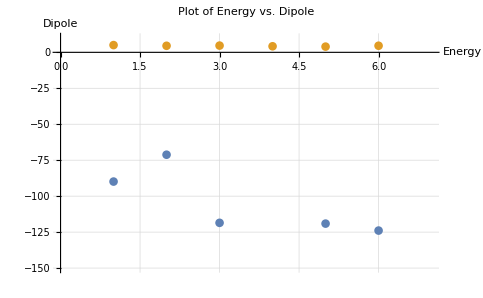

```mathematica
engDipole = Transpose[{energy,dipole}];
ListPlot[{energy,dipole}, PlotRange-> {{0,7},{10,-150}},PlotLabel -> "Plot of Energy vs. Dipole", AxesLabel -> {"Energy","Dipole"}, GridLines-> Automatic,LabelStyle->{FontFamily->"Times New Roman",13,GrayLevel[0]}]
```

Regression Analysis:

```mathematica
model = LinearModelFit[engDipole,x,x]
Normal[model]
```

FittedModel[5.22431+0.00634042 x]

5.22431+0.00634042 x

Correlation Coefficient (R^2):

```mathematica
rval1=Correlation[energy,dipole];
Print[rval1^2]
```

0.265162

Genez very much appreciates the opportunity to conduct this work and hopes that the results are satisfactory. We look forward to a long working relationship with the Vertextin, and wish your company success in its  drug discovery ventures.

I certify that this work was completed by me on February 5, 2021.  All references and resources are cited.  Assistance was provided by NAME OF PERSON(S) (if any)
  Electronic signature: -Graphics-